# Analytical solution of the test ODE

## Mass-spring-damper

### ODE

```mathematica
ode={v[t],-k q[t]-2κ v[t]+u}
```

{v[t],u-k q[t]-2 κ v[t]}

### ODE sensitivities

```mathematica
J=D[ode,{{q[t],v[t],u}}]//FullSimplify;
J//MatrixForm
seed=Array[S,{2,3}]~Join~Join[ConstantArray[0,{1,2}],IdentityMatrix[1],2];
seed//MatrixForm
Sf=J.seed;
Sf//MatrixForm
```

(0 | 1 | 0
-k | -2 κ | 1)

(S[1,1] | S[1,2] | S[1,3]
S[2,1] | S[2,2] | S[2,3]
0 | 0 | 1)

(S[2,1] | S[2,2] | S[2,3]
-k S[1,1]-2 κ S[2,1] | -k S[1,2]-2 κ S[2,2] | 1-k S[1,3]-2 κ S[2,3])

### IVP solution

```mathematica
sol=DSolve[{q'[t]==ode⟦1⟧,v'[t]==ode⟦2⟧,q[0]==q0,v[0]==v0},{q[t],v[t]},t]⟦1⟧//FullSimplify
```

{q[t]→1/(2 k √(-k+κ^2))ⅇ^(-t (κ+√(-k+κ^2))) (-u ((-1+ⅇ^(2 t √(-k+κ^2))) κ+(1+ⅇ^(2 t √(-k+κ^2))-2 ⅇ^(t (κ+√(-k+κ^2)))) √(-k+κ^2))+k ((-1+ⅇ^(2 t √(-k+κ^2))) v0-q0 κ+q0 (√(-k+κ^2)+ⅇ^(2 t √(-k+κ^2)) (κ+√(-k+κ^2))))),v[t]→(ⅇ^(-t κ) (v0 √(-k+κ^2) Cosh[t √(-k+κ^2)]+(-k q0+u-v0 κ) Sinh[t √(-k+κ^2)]))/(√(-k+κ^2))}

```mathematica
sol1=sol/.{√(-k+κ^2)->s,1/√(-k+κ^2)->1/s}
FullSimplify[sol1,s∈Reals]
FullSimplify[sol1/.s->ⅈ ω,ω∈Reals]
```

{q[t]→1/(2 k s)ⅇ^(-t (s+κ)) (-u ((1+ⅇ^(2 s t)-2 ⅇ^(t (s+κ))) s+(-1+ⅇ^(2 s t)) κ)+k ((-1+ⅇ^(2 s t)) v0-q0 κ+q0 (s+ⅇ^(2 s t) (s+κ)))),v[t]→(ⅇ^(-t κ) (s v0 Cosh[s t]+(-k q0+u-v0 κ) Sinh[s t]))/s}

{q[t]→(ⅇ^(-t (s+κ)) (-u ((1+ⅇ^(2 s t)-2 ⅇ^(t (s+κ))) s+(-1+ⅇ^(2 s t)) κ)+k (q0 s-v0-q0 κ+ⅇ^(2 s t) (v0+q0 (s+κ)))))/(2 k s),v[t]→(ⅇ^(-t κ) (s v0 Cosh[s t]+(-k q0+u-v0 κ) Sinh[s t]))/s}

{q[t]→1/(2 k ω)ⅇ^(-t (κ+ⅈ ω)) (u (-ⅈ κ-ω+2 ⅇ^(t (κ+ⅈ ω)) ω-ⅇ^(2 ⅈ t ω) (-ⅈ κ+ω))+2 ⅇ^(ⅈ t ω) k (q0 ω Cos[t ω]+(v0+q0 κ) Sin[t ω])),v[t]→(ⅇ^(-t κ) (v0 ω Cos[t ω]+(-k q0+u-v0 κ) Sin[t ω]))/ω}

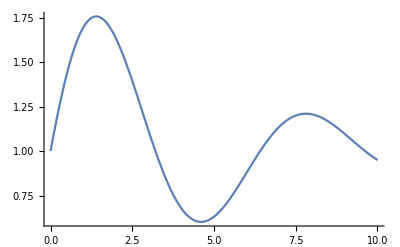

{q[5.]→0.631052+1.38778×10^-17 ⅈ,v[5.]→0.142035+0. ⅈ}

```mathematica
Plot[q[t]/.sol/.{q0->1,v0->1,k->1,κ->0.2,u->1},{t,0,10}]
sol/.{q0->1,v0->1,k->1,κ->0.2,u->1,t->5.}
```

### IVP solution sensitivities

```mathematica
D[{q[t],v[t]}/.sol1,{{q0,v0,u}}]//FullSimplify//MatrixForm
%/.s->√(-k+κ^2)/.{k->1,κ->0.2,t->5}
```

((ⅇ^(-t κ) (s Cosh[s t]+κ Sinh[s t]))/s | (ⅇ^(-t (s+κ)) (-1+ⅇ^(2 s t)))/(2 s) | (s-ⅇ^(-t κ) (s Cosh[s t]+κ Sinh[s t]))/(k s)
-(ⅇ^(-t κ) k Sinh[s t])/s | (ⅇ^(-t κ) (s Cosh[s t]-κ Sinh[s t]))/s | (ⅇ^(-t κ) Sinh[s t])/s)

{{-0.00554445+0. ⅈ,-0.368948+0. ⅈ,1.00554+0. ⅈ},{0.368948+0. ⅈ,0.142035+0. ⅈ,-0.368948+0. ⅈ}}

### Residual

```mathematica
r={v[t]u,u}
```

{u v[t],u}

#### Sensitivity of the residual

```mathematica
J=D[r,{{q[t],v[t],u}}]
J.seed//MatrixForm
```

{{0,u,v[t]},{0,0,1}}

(u S[2,1] | u S[2,2] | u S[2,3]+v[t]
0 | 0 | 1)

#### Integral of the Lagrange term

```mathematica
V=1/2∫_0^T r.rⅆt/.sol1//FullSimplify
```

1/(8 s^2 (s-κ) κ (s+κ))ⅇ^(-2 T κ) u^2 ((s-κ) (s+κ) (k q0-u+v0 (-s+κ)) (k q0-u+v0 (s+κ))-ⅇ^(2 T κ) s^2 ((-k q0+u)^2+(v0^2+4 T κ) (-s^2+κ^2))+κ (k^2 q0^2 κ+κ (u-v0 κ)^2+s^2 v0 (2 u-v0 κ)-2 k q0 (s^2 v0+κ (u-v0 κ))) Cosh[2 s T]+s κ ((-k q0+u)^2+v0^2 (s-κ) (s+κ)) Sinh[2 s T])

```mathematica
V/.s->√(-k+κ^2)/.{q0->1,v0->1,k->1,κ->0.2,u->1,T->5.}
```

3.02731-7.51262×10^-17 ⅈ

#### Gradient of the Integral of the Lagrange term

```mathematica
D[V,{{q0,v0,u}}]//FullSimplify
```

{1/(4 s^2 κ (-s+κ) (s+κ))ⅇ^(-2 T κ) k u^2 (ⅇ^(2 T κ) s^2 (k q0-u)+(k q0-u+v0 κ) (-s^2+κ^2)+κ (s^2 v0+κ (-k q0+u-v0 κ)) Cosh[2 s T]+s (-k q0+u) κ Sinh[2 s T]),1/(4 s^2 κ)ⅇ^(-2 T κ) u^2 ((-1+ⅇ^(2 T κ)) s^2 v0+κ (k q0-u+v0 κ)+κ (-k q0+u-v0 κ) Cosh[2 s T]+s v0 κ Sinh[2 s T]),1/(4 s^2 κ (-s+κ) (s+κ))ⅇ^(-2 T κ) u ((s-κ) (s+κ) (s^2 v0^2-(k q0-2 u+v0 κ) (k q0-u+v0 κ))+ⅇ^(2 T κ) s^2 ((k q0-2 u) (k q0-u)+(v0^2+4 T κ) (-s^2+κ^2))-κ (k^2 q0^2 κ+s^2 v0 (3 u-v0 κ)+κ (-2 u+v0 κ) (-u+v0 κ)+k q0 (-2 s^2 v0+κ (-3 u+2 v0 κ))) Cosh[2 s T]-s κ ((k q0-2 u) (k q0-u)+v0^2 (s-κ) (s+κ)) Sinh[2 s T])}

#### Gauss-Newton approximation of the Lagrange term

```mathematica
H=Transpose[J].J;
H//MatrixForm
```

(0 | 0 | 0
0 | u^2 | u v[t]
0 | u v[t] | 1+v[t]^2)

#### Integral of the Gauss-Newton approximation of the Lagrange term

```mathematica
S[t]=D[{q[t],v[t],u}/.sol1,{{q0,v0,u}}];
HH=Transpose[S[t]].H.S[t]/.sol1//FullSimplify;
HH//MatrixForm
```

((ⅇ^(-2 t κ) k^2 u^2 Sinh[s t]^2)/s^2 | (ⅇ^(-2 t κ) k u^2 Sinh[s t] (-s Cosh[s t]+κ Sinh[s t]))/s^2 | (ⅇ^(-2 t κ) k u (k q0-2 u+v0 κ-s v0 Coth[s t]) Sinh[s t]^2)/s^2
(ⅇ^(-2 t κ) k u^2 Sinh[s t] (-s Cosh[s t]+κ Sinh[s t]))/s^2 | (ⅇ^(-2 t κ) u^2 (s Cosh[s t]-κ Sinh[s t])^2)/s^2 | (ⅇ^(-2 t κ) u (s Cosh[s t]-κ Sinh[s t]) (s v0 Cosh[s t]-(k q0-2 u+v0 κ) Sinh[s t]))/s^2
(ⅇ^(-2 t κ) k u (k q0-2 u+v0 κ-s v0 Coth[s t]) Sinh[s t]^2)/s^2 | (ⅇ^(-2 t κ) u (s Cosh[s t]-κ Sinh[s t]) (s v0 Cosh[s t]-(k q0-2 u+v0 κ) Sinh[s t]))/s^2 | (ⅇ^(-2 t κ) (s^2 v0^2 Cosh[s t]^2+(k q0-2 u+v0 κ)^2 Sinh[s t]^2+s (ⅇ^(2 t κ) s-v0 (k q0-2 u+v0 κ) Sinh[2 s t])))/s^2)

```mathematica
HH=∫_0^T Transpose[S[t]].H.S[t]ⅆt/.sol1
```

{{(ⅇ^(-2 T κ) k^2 u^2 ((-1+ⅇ^(2 T κ)) s^2+κ^2-κ (κ Cosh[2 s T]+s Sinh[2 s T])))/(4 s^2 (-s^2 κ+κ^3)),-(ⅇ^(-2 T κ) k u^2 Sinh[s T]^2)/(2 s^2),1/(4 s^2 κ (-s+κ) (s+κ))ⅇ^(-2 T κ) k u (ⅇ^(2 T κ) s^2 (k q0-2 u)+(k q0-2 u+v0 κ) (-s^2+κ^2)+κ (s^2 v0-κ (k q0-2 u+v0 κ)) Cosh[2 s T]+s (-k q0+2 u) κ Sinh[2 s T])},{-(ⅇ^(-2 T κ) k u^2 Sinh[s T]^2)/(2 s^2),(ⅇ^(-2 T κ) u^2 ((-1+ⅇ^(2 T κ)) s^2+κ^2-κ^2 Cosh[2 s T]+s κ Sinh[2 s T]))/(4 s^2 κ),1/(4 s^2 κ)ⅇ^(-2 T κ) u ((-1+ⅇ^(2 T κ)) s^2 v0+κ (k q0-2 u+v0 κ)-κ (k q0-2 u+v0 κ) Cosh[2 s T]+s v0 κ Sinh[2 s T])},{1/(4 s^2 κ (-s+κ) (s+κ))ⅇ^(-2 T κ) k u (ⅇ^(2 T κ) s^2 (k q0-2 u)+(k q0-2 u+v0 κ) (-s^2+κ^2)+κ (s^2 v0-κ (k q0-2 u+v0 κ)) Cosh[2 s T]+s (-k q0+2 u) κ Sinh[2 s T]),1/(4 s^2 κ)ⅇ^(-2 T κ) u ((-1+ⅇ^(2 T κ)) s^2 v0+κ (k q0-2 u+v0 κ)-κ (k q0-2 u+v0 κ) Cosh[2 s T]+s v0 κ Sinh[2 s T]),1/s^2(-1/(4 κ (-s+κ) (s+κ))(-(s^2-κ^2) (k^2 q0^2+4 u^2-s^2 v0^2-4 u v0 κ+v0^2 κ^2+k q0 (-4 u+2 v0 κ))-κ (k^2 q0^2 κ+s^2 v0 (4 u-v0 κ)+κ (-2 u+v0 κ)^2-2 k q0 (s^2 v0+κ (2 u-v0 κ))))+1/(4 κ (-s+κ) (s+κ))ⅇ^(-2 T κ) (-(s^2-κ^2) (k^2 q0^2+4 u^2-s^2 v0^2+4 ⅇ^(2 T κ) s^2 T κ-4 u v0 κ+v0^2 κ^2+k q0 (-4 u+2 v0 κ))-κ (k^2 q0^2 κ+s^2 v0 (4 u-v0 κ)+κ (-2 u+v0 κ)^2-2 k q0 (s^2 v0+κ (2 u-v0 κ))) Cosh[2 s T]-s κ (k^2 q0^2-4 k q0 u+4 u^2+v0^2 (s^2-κ^2)) Sinh[2 s T]))}}

```mathematica
HH//FullSimplify//MatrixForm
```

((ⅇ^(-2 T κ) k^2 u^2 ((-1+ⅇ^(2 T κ)) s^2+κ^2-κ (κ Cosh[2 s T]+s Sinh[2 s T])))/(4 s^2 (-s^2 κ+κ^3)) | -(ⅇ^(-2 T κ) k u^2 Sinh[s T]^2)/(2 s^2) | (ⅇ^(-2 T κ) k u (ⅇ^(2 T κ) s^2 (k q0-2 u)+(k q0-2 u+v0 κ) (-s^2+κ^2)+κ (s^2 v0-κ (k q0-2 u+v0 κ)) Cosh[2 s T]+s (-k q0+2 u) κ Sinh[2 s T]))/(4 s^2 κ (-s+κ) (s+κ))
-(ⅇ^(-2 T κ) k u^2 Sinh[s T]^2)/(2 s^2) | (ⅇ^(-2 T κ) u^2 ((-1+ⅇ^(2 T κ)) s^2+κ^2-κ^2 Cosh[2 s T]+s κ Sinh[2 s T]))/(4 s^2 κ) | (ⅇ^(-2 T κ) u ((-1+ⅇ^(2 T κ)) s^2 v0+κ (k q0-2 u+v0 κ)-κ (k q0-2 u+v0 κ) Cosh[2 s T]+s v0 κ Sinh[2 s T]))/(4 s^2 κ)
(ⅇ^(-2 T κ) k u (ⅇ^(2 T κ) s^2 (k q0-2 u)+(k q0-2 u+v0 κ) (-s^2+κ^2)+κ (s^2 v0-κ (k q0-2 u+v0 κ)) Cosh[2 s T]+s (-k q0+2 u) κ Sinh[2 s T]))/(4 s^2 κ (-s+κ) (s+κ)) | (ⅇ^(-2 T κ) u ((-1+ⅇ^(2 T κ)) s^2 v0+κ (k q0-2 u+v0 κ)-κ (k q0-2 u+v0 κ) Cosh[2 s T]+s v0 κ Sinh[2 s T]))/(4 s^2 κ) | (ⅇ^(-2 T κ) ((s-κ) (s+κ) (k q0-2 u+v0 (-s+κ)) (k q0-2 u+v0 (s+κ))+ⅇ^(2 T κ) s^2 (-(k q0-2 u)^2+(s-κ) (s+κ) (v0^2+4 T κ))+κ (k^2 q0^2 κ+s^2 v0 (4 u-v0 κ)+κ (-2 u+v0 κ)^2-2 k q0 (2 u κ+v0 (s-κ) (s+κ))) Cosh[2 s T]+s κ ((k q0-2 u)^2+v0^2 (s-κ) (s+κ)) Sinh[2 s T]))/(4 s^2 (s-κ) κ (s+κ)))

## Exponent

### ODE

```mathematica
ode={-u x[t]}
```

{-u x[t]}

### ODE sensitivities

```mathematica
J=D[ode,{{x[t],u}}]//FullSimplify;
J//MatrixForm
seed=Array[S,{1,2}]~Join~Join[ConstantArray[0,{1,1}],IdentityMatrix[1],2];
seed//MatrixForm
Sf=J.seed;
Sf
```

(-u | -x[t])

(S[1,1] | S[1,2]
0 | 1)

{{-u S[1,1],-u S[1,2]-x[t]}}

### IVP solution

```mathematica
sol=DSolve[{x'[t]==ode⟦1⟧,x[0]==x0},{x[t]},t]⟦1⟧//FullSimplify
```

{x[t]→ⅇ^(-t u) x0}

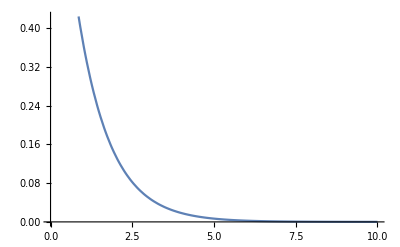

{x[5.]→0.00673795}

```mathematica
Plot[x[t]/.sol/.{x0->1,u->1},{t,0,10}]
sol/.{x0->1,u->1,t->5.}
```

### IVP solution sensitivities

```mathematica
D[{x[t]}/.sol,{{x0,u}}]//FullSimplify
```

{{ⅇ^(-t u),-ⅇ^(-t u) t x0}}

### Residual

```mathematica
r={x[t]}
```

{x[t]}

#### Sensitivity of the residual

```mathematica
J=D[r,{{x[t],u}}]
J.seed//MatrixForm
```

{{1,0}}

(S[1,1] | S[1,2])

#### Integral of the Lagrange term

```mathematica
V=1/2∫_0^T r.rⅆt/.sol//FullSimplify
```

-((-1+ⅇ^(-2 T u)) x0^2)/(4 u)

```mathematica
V/.{x0->1,u->1,T->5.}
```

0.249989

#### Gradient of the Integral of the Lagrange term

```mathematica
D[V,{{x0,u}}]//FullSimplify
```

{-((-1+ⅇ^(-2 T u)) x0)/(2 u),-(ⅇ^(-2 T u) (-1+ⅇ^(2 T u)-2 T u) x0^2)/(4 u^2)}

#### Gauss-Newton approximation of the Lagrange term

```mathematica
H=Transpose[J].J;
H//MatrixForm
```

(1 | 0
0 | 0)

#### Integral of the Gauss-Newton approximation of the Lagrange term

```mathematica
S[t]=D[{x[t],u}/.sol,{{x0,u}}];
HH=Transpose[S[t]].H.S[t]/.sol//FullSimplify;
HH//MatrixForm
```

(ⅇ^(-2 t u) | -ⅇ^(-2 t u) t x0
-ⅇ^(-2 t u) t x0 | ⅇ^(-2 t u) t^2 x0^2)

```mathematica
HH=∫_0^T Transpose[S[t]].H.S[t]ⅆt/.sol
```

{{-(-1+ⅇ^(-2 T u))/(2 u),-(ⅇ^(-2 T u) (-1+ⅇ^(2 T u)-2 T u) x0)/(4 u^2)},{-(ⅇ^(-2 T u) (-1+ⅇ^(2 T u)-2 T u) x0)/(4 u^2),((1+ⅇ^(-2 T u) (-1-2 T u (1+T u))) x0^2)/(4 u^3)}}

```mathematica
HH//FullSimplify//MatrixForm
```

(-(-1+ⅇ^(-2 T u))/(2 u) | -(ⅇ^(-2 T u) (-1+ⅇ^(2 T u)-2 T u) x0)/(4 u^2)
-(ⅇ^(-2 T u) (-1+ⅇ^(2 T u)-2 T u) x0)/(4 u^2) | ((1+ⅇ^(-2 T u) (-1-2 T u (1+T u))) x0^2)/(4 u^3))